```mathematica
FullSimplify[2*I/L*Sum[Sin[2*Pi*f*l*P-θ]*Exp[-2*Pi*I*f*l*P],{l,1,L}]]
```

ⅇ^(-ⅈ θ)-(ⅇ^(ⅈ θ) (-1+ⅇ^(-4 ⅈ f L P π)))/(L-ⅇ^(4 ⅈ f P π) L)

```mathematica
(Exp[-4*I*f*L*P*Pi]-1)/(L-Exp[4*I*f*P*Pi]*L) ==Exp[-4*Pi*I*f*P*L]*Sin[4*Pi*f*P*L]/Sin[4*Pi*f*P]/L
```

(-1+ⅇ^(-4 ⅈ f π))/(1-ⅇ^(4 ⅈ f π))==ⅇ^(-4 ⅈ f π)

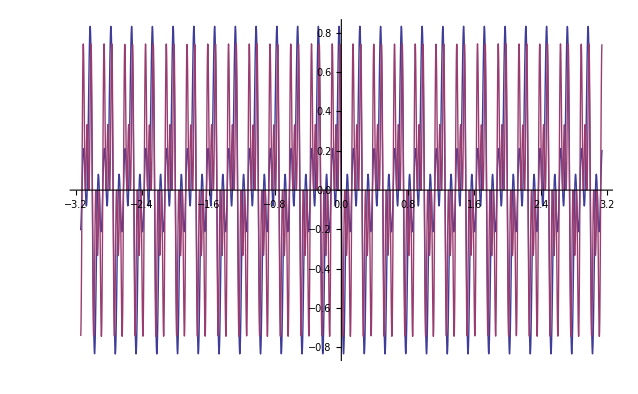

```mathematica
L=3;
P=2;
f1[f_]:= (Exp[-4*I*f*L*P*Pi]-1)/(L-Exp[4*I*f*P*Pi]*L);
f2[f_]:=Exp[-4*Pi*I*f*P*L]*Sin[4*Pi*f*P*L]/Sin[4*Pi*f*P]/L;
Plot[{Im[f1[x]],Im[f2[x]]},{x,-Pi,Pi}]
```

```mathematica
Clear[L,P];
FullSimplify[(Exp[-4*I*f*L*P*Pi]-1)/(L-Exp[4*I*f*P*Pi]*L)]
```

(-1+ⅇ^(-4 ⅈ f L P π))/(L-ⅇ^(4 ⅈ f P π) L)

```mathematica
FullSimplify[(Exp[-4*I*f*L*P*Pi]-1)/(L-Exp[4*I*f*P*Pi]*L)==Exp[-2*I*f*L*P*Pi]*(Exp[-2*I*f*L*P*Pi]-Exp[2*I*f*L*P*Pi])/(L-Exp[4*I*f*P*Pi]*L)]
```

True

```mathematica
FullSimplify[(Exp[-4*I*f*L*P*Pi]-1)/(L-Exp[4*I*f*P*Pi]*L)==Exp[-2*I*f*L*P*Pi]*(Exp[-2*I*f*L*P*Pi]-Exp[2*I*f*L*P*Pi])/Exp[2*I*f*P*Pi]/(Exp[-2*I*f*P*Pi]*L-Exp[2*I*f*P*Pi]*L)]
```

True

```mathematica
FullSimplify[(Exp[-4*I*f*L*P*Pi]-1)/(L-Exp[4*I*f*P*Pi]*L)==Exp[-2*I*f*P*Pi*(L+1)]*(Exp[-2*I*f*L*P*Pi]-Exp[2*I*f*L*P*Pi])/(Exp[-2*I*f*P*Pi]*L-Exp[2*I*f*P*Pi]*L)]
```

True

```mathematica
FullSimplify[(Exp[-4*I*f*L*P*Pi]-1)/(L-Exp[4*I*f*P*Pi]*L)==Exp[-2*I*f*P*Pi*(L+1)]*Sin[2*f*L*P*Pi]/L/Sin[2*f*P*Pi]]
```

True

```mathematica
Exp[-2*I*f*P*Pi*(L+1)]*Sin[2*f*L*P*Pi]/L/Sin[2*f*P*Pi]
```

(ⅇ^(-2 ⅈ f (1+L) P π) Csc[2 f P π] Sin[2 f L P π])/L